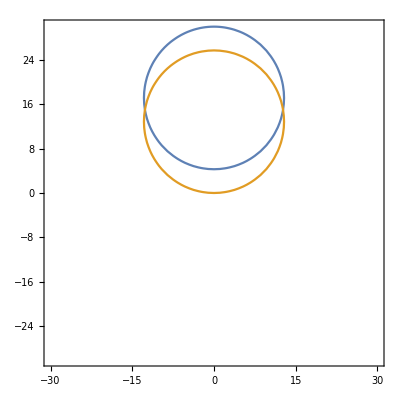

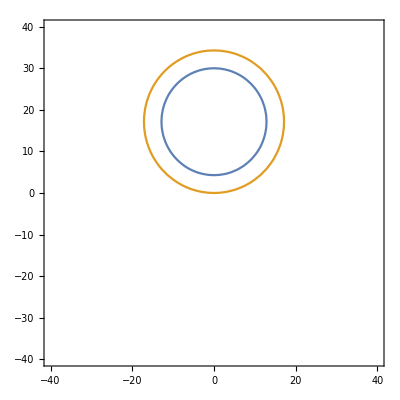

```mathematica
Q=30;
P=0;
En=Q^2+P^2*4/3;
K=Q+P;
ContourPlot[{x^2*7/3+y^2+4/3*(K-y)^2==En,x^2*7/3+(K-y)^2+4/3*(y)^2==En},{x,-Q,Q},{y,-Q,Q}]
ContourPlot[{x^2*7/3+y^2+4/3*(K-y)^2==En,(3/4*x)^2*7/3+(K-3/4*y)^2+4/3*(3/4*y)^2==En},{x,-4/3*Q,4/3*Q},{y,-4/3*Q,4/3*Q}]
```

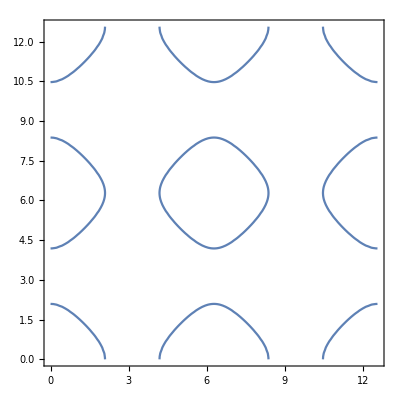

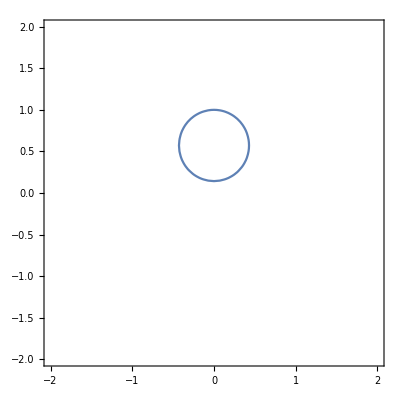

```mathematica
ContourPlot[Cos[x]+Cos[y]==1/2,{x,0,4 Pi},{y,0,4 Pi}]
```

```mathematica
Graphics3D[{Opacity[.3],Sphere[],Sphere[{0,0,2}]}]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{Opacity[.3],Sphere[{0,0,0}],Sphere[{0,0,2}]}],Graphics3D[Ellipsoid[{0,0,0},1./4*{4,3,2}]],ParametricPlot3D[{{1/Sqrt[2]*Cos[u],-Sin[u],1/Sqrt[2]*Cos[u]+2},{1/Sqrt[2]*Cos[u],-Sin[u],1/Sqrt[2]*Cos[u]},{Sin[u],Cos[u],0},{Sin[u],Cos[u],2}},{u,0,20},PlotStyle->{Blue,Blue,Red,Red}],Boxed->False]
```

-Graphics3D-

```mathematica
Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}]
```

-Graphics3D-